```mathematica
(*1*)
f[x_]=(x-3)*ⅇ^(Sin[x^2+2]^(1/3));
x0=5.12;
```

```mathematica
D1=D[f[x],x]/.x->x0//N
D2=D[f[x],{x,2}]/.x->x0//N
```

-68.2989

-6507.72

```mathematica
h1=0.001;
Delta1=f[x0 + h1]-f[x0];
Delta2=f[x0+2*h1]-2*f[x0+h1]+f[x0];
Delta3=f[x0+3*h1]-3*f[x0+2*h1]+3*f[x0+h1]-f[x0];
D1=1/h1*(Delta1-1/2*Delta2+1/3*Delta3)  // N
D2=1/h1^2*(Delta2-Delta3) // N
```

-68.8046

-4786.34

```mathematica
h2=0.0001;
Delta1=f[x0+h2]-f[x0];
Delta2=f[x0+2*h2]-2*f[x0+h2]+f[x0];
Delta3=f[x0+3*h2]-3*f[x0+2*h2]+3*f[x0+h2]-f[x0];
D1prime=1/h2*(Delta1-1/2*Delta2+1/3*Delta3) // N
D2prime=1/h2^2*(Delta2-Delta3) // N
```

-68.2991

-6499.88

```mathematica
(*2*)
```

```mathematica
f2[x_]=(Cos[2x+3]+1)^(Log[3x+7]);
a = -1;
b = 3;
h=0.2;
Data=Table[{i,(f2[i+h]-f2[i-h])/(2h)},{i,a,b,h}]//N;
Data//TableForm
```

-1. | -2.04443
-0.8 | -2.91551
-0.6 | -2.65183
-0.4 | -1.56685
-0.2 | -0.524553
0. | -0.0652007
0.2 | 0.0924852
0.4 | 0.57492
0.6 | 1.82225
0.8 | 3.86538
1. | 6.0618
1.2 | 7.12784
1.4 | 5.79705
1.6 | 1.86596
1.8 | -3.21056
2. | -6.97808
2.2 | -7.6893
2.4 | -5.63972
2.6 | -2.76195
2.8 | -0.815753
3. | -0.112093

```mathematica
f3[x_]=D[f2[x],x];
```

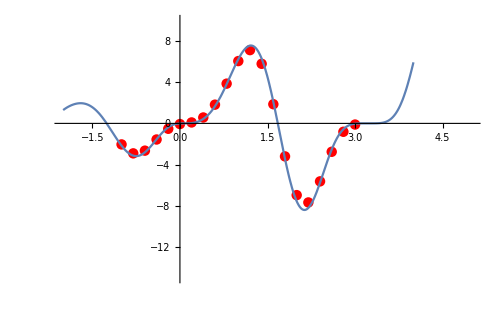

```mathematica
Show[ListPlot[Data,PlotStyle->{Red,PointSize[0.015]}],Plot[f3[x],{x,-2,4}],PlotRange->{{-2,5},{-15,10}}]
```

```mathematica
(*3*)
(* a, n=8 *)
a = 1.2;
b = 2;
n=8;
fNEW[x_]=(√(4x^2+1.5))/(4x+√(0.6x^2+3));
```

```mathematica
Integrate[fNEW[x],{x,a,b}]//N
```

0.321351

```mathematica
Integral1=0;
Do[Integral1+=(fNEW[a+i*h]+fNEW[a+(i-1)*h])/2,{i,1,n}];
Integral1*=(b-a)/n;
Integral1
```

0.323838

```mathematica
Integral2 = 0;
Do[Integral2+=fNEW[a+i*h],{i,1,n-1}];
Integral2+=(fNEW[a]+fNEW[b])/2;
Integral2*=(b-a)/n;
Integral2
```

0.32359

```mathematica
(* n = 10*)
n = 10;
Integral3=0;
Do[Integral3+=(fNEW[a+i*h]+fNEW[a+(i-1)*h])/2,{i,1,n}];
Integral3*=(b-a)/n;
Integral3
```

0.324832

```mathematica
Integral4 = 0;
Do[Integral4+=fNEW[a+i*h],{i,1,n-1}];
Integral4+=(fNEW[a]+fNEW[b])/2;
Integral4*=(b-a)/n;
Integral4
```

0.324569

```mathematica
Rich1=Integral3+8^2/(10^2-8^2)*(Integral3-Integral1)
```

0.326598

```mathematica
Rich2=Integral4+8^2/(10^2-8^2)*(Integral4-Integral2)
```

0.326308

```mathematica
(*4*)

data={
{0.2,1.2336},
{0.25,1.2680},
{0.3,1.3702},
{0.35,1.3944},
{0.4,1.5219},
{0.45,1.5334},
{0.5,1.6904},
{0.55,1.6862},
{0.6,1.8776},
{0.65,1.8542},
{0.7,2.0854},
{0.75,2.0390},
{0.8,2.3163},
{0.85,2.2423},
{0.9,2.5728},
{0.95,2.4657},
{1,2.8576}
};
DataY = {1.2336, 1.2680, 1.3702, 1.3944,1.5219,1.5334,1.6904,1.6862,1.8776,1.8542,2.0854,2.0390,2.3163,2.2423,2.5728,2.4657,2.8576};
```

```mathematica
a=0.2;
b=1;
n=8;
h=(b-a)/(2n);
```

```mathematica
Sum1=0;
Sum2=0;
Do[Sum1+=DataY[[i]],{i,2,2n,2}];
Do[Sum2+=DataY[[i]],{i,3,2(n-1),2}];
h/3*(DataY[[2n+1]]+DataY[[1]] +4 *Sum1  +2 * Sum2)
```

1.39579

```mathematica
a=0.2;
b=1;
n=4;
h=(b-a)/(2n);
Sum1=0;
Sum2=0;
Do[Sum1+=DataY[[i]],{i,3,4n,4}];
Do[Sum2+=DataY[[i]],{i,5,4(n-1),4}];
h/3*(DataY[[4n+1]]+DataY[[1]] +4 *Sum1  +2 * Sum2)
```

1.39218

```mathematica
(*5*)
fNEWNEW[x_]= √(2x+1)Log[x+3];
n=6;
a=1;
b=2.1;
LegendreP[n,t];
sl=NSolve[LegendreP[n,t]==0,t];
tt=t/.sl;
T=Table[If[i==1,1,(tt[[j]])^(i-1)],{i,n},{j,n}];
MatrixForm[T];
B=Table[If[EvenQ[i]==True,0,2/i],{i,n}]//N;
A=LinearSolve[T,B];
int=(b-a)/2*∑_(i=1)^n A[[i]]*fNEWNEW[(b+a)/2+(b-a)/2*tt[[i]]]
```

3.37115

```mathematica
NIntegrate[fNEWNEW[x],{x,a,b}]
```

3.37115